```mathematica
Clear["Global`*"]
```

```mathematica
Pin={{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}(*Point input*)
```

{{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}

```mathematica
UndirectedGIn=CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"];
```

```mathematica
Ruleg={1->2,1->3,4->1,1->5,3->2,4->2,2->5,4->3,3->5,5->4}
```

{1→2,1→3,4→1,1→5,3→2,4→2,2→5,4→3,3→5,5→4}

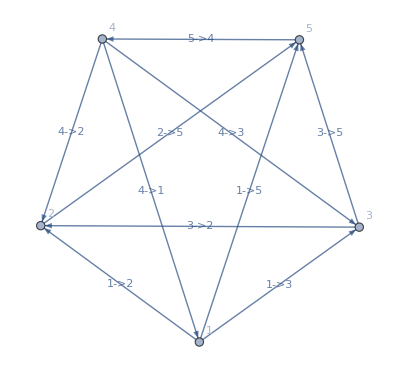

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

### Designation of Fund Loop

```mathematica
RuleFundLoop={{5->4,4->1,1->5},{3->5,5->1,1->3},{4->3,3->1,1->4},{2->5,5->1,1->2},{4->2,2->1,1->4},{3->2,2->1,1->3}}
```

{{5→4,4→1,1→5},{3→5,5→1,1→3},{4→3,3→1,1→4},{2→5,5→1,1→2},{4→2,2→1,1→4},{3→2,2→1,1→3}}

```mathematica
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[RuleFundLoop]}
]
```

{{5→1,4→5,1→4},{3→1,5→3,1→5},{4→1,3→4,1→3},{2→1,5→2,1→5},{4→1,2→4,1→2},{3→1,2→3,1→2}}

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[RuleFundLoop]}]
```

(0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{√5,2.06155,4.94975,5,1.80278,2.91548,2 √5,3.3541,3.04138,3.80789}

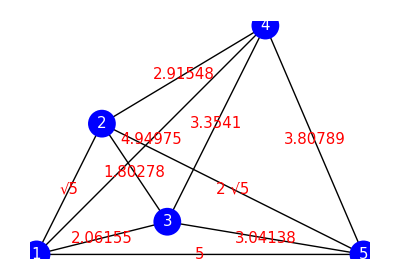

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[PD[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{√5,0,0,0,0,0,0,0,0,0},{0.,2.06155,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,4.94975,0.,0.,0.,0.,0.,0.,0.},{0,0,0,5,0,0,0,0,0,0},{0.,0.,0.,0.,1.80278,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.91548,0.,0.,0.,0.},{0,0,0,0,0,0,2 √5,0,0,0},{0.,0.,0.,0.,0.,0.,0.,3.3541,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,3.04138,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,3.80789}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Point *)
```

{{{5,0},{3.5,3.5},{0,0}},{{2,0.5},{5,0},{0,0}},{{3.5,3.5},{2,0.5},{0,0}},{{1,2},{5,0},{0,0}},{{3.5,3.5},{1,2},{0,0}},{{2,0.5},{1,2},{0,0}}}

```mathematica
{{{5,0},{0,0},{3.5,3.5}},{{5,0},{0,0},{2,0.5}},{{3.5,3.5},{0,0},{2,0.5}},{{5,0},{0,0},{1,2}},{{3.5,3.5},{0,0},{1,2}},{{2,0.5},{0,0},{1,2}}}
```

```mathematica
RuleFundLoop
```

{{5→4,4→1,1→5},{3→5,5→1,1→3},{4→3,3→1,1→4},{2→5,5→1,1→2},{4→2,2→1,1→4},{3→2,2→1,1→3}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}](* 右回りならば負、左回りならば正 *)
```

{1,-1,-1,-1,1,1}

```mathematica
{-1,1,1,1,-1,-1}
```

```mathematica
{1,1,-1,1,1,1}
```

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Area *)
```

{8.75,1.25,2.625,5,1.75,1.75}

```mathematica
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}](* 誘導起電力は右回りなら負、左回りなら正 *)
```

{8.75,-1.25,-2.625,-5,1.75,1.75}

```mathematica
{8.75,-1.25,-2.625,-5,1.7499999999999993,1.75}
```

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.623285,0.32532,0.348797,0.646762,-0.174382,0.714377,-0.0832895,-0.0679409,0.43176,0.995233}

```mathematica
{-0.6232848767277974,0.32531952701781036,0.34879677341835547,0.6467621231283425,-0.1743815109969175,0.7143768736322502,-0.08328951409246461,-0.06794088853799715,0.43176014947673075,0.9952327585126084}
```

```mathematica
{-0.6232848767277975,0.32531952701781036,0.3487967734183554,0.6467621231283425,-0.1743815109969175,0.7143768736322504,-0.08328951409246461,-0.06794088853799721,0.43176014947673075,0.9952327585126086}
```

```mathematica
Reverse[Ordering[Abs[Curr]]]
```

{10,6,4,1,9,3,2,5,7,8}

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

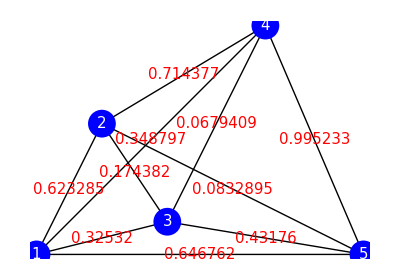

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

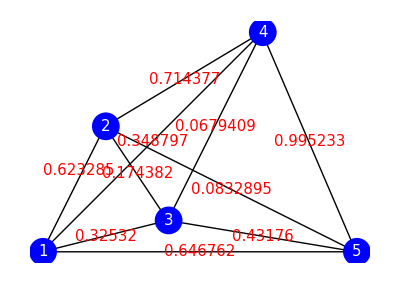

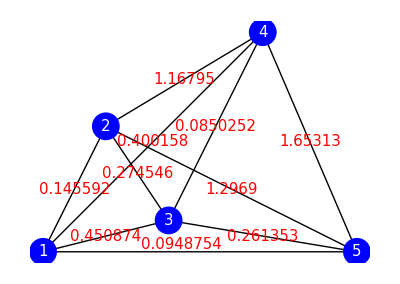

```mathematica
For[j=3,
!MemberQ[Table[Length[Cycle[[i]]],{i,Range[Length[Cycle]]}],Length[Pin]],
j++,
Cycle=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[j]]]]]],
Infinity,All];
j++;
]
Cycle[[
FirstPosition[Table[Length[Cycle[[i]]],{i,Range[Length[Cycle]]}],Length[Pin]][[1]]
]]
```

{4->5,5->2,2->3,3->1,1->4}